#### generate

```mathematica
SystemOpen[NotebookDirectory[]]
```

```mathematica
LoopMomenta={l1,l2,l3};
ExternalMomenta={k1,k2,k3,k4};
Propagators={l1^2,(-k1+l1)^2,(-k1-k2+l1)^2,(-k1-k2-k3+l1)^2,l2^2,(-k1-k2-k3+l2)^2,l3^2,(-k1-k2-k3+l3)^2,(-k1-k2-k3-k4+l3)^2,(l1-l2)^2,(l2-l3)^2,(-k1-k2-k3-k4+l1)^2,(-k1+l2)^2,(-k1-k2+l2)^2,(-k1-k2-k3-k4+l2)^2,(-k1+l3)^2,(-k1-k2+l3)^2,(l1-l3)^2};
Kinematics={k1^2->0,k2^2->0,k3^2->0,k4^2->0,k1 k2->s12/2,k1 k3->1/2(-s12-s23+s45),k1 k4->1/2(-s15+s23-s45),k2 k3->s23/2,k2 k4->1/2(s15-s23-s34),k3 k4->s34/2};Numerics={s12->-1/13,s23->-1/97,s34->-1/73,s45->7,s15->213};
```

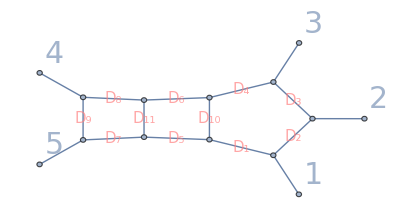
```mathematica
SetDirectory[NotebookDirectory[]]
topgraph=-Graphics-;
mis=ToExpression[StringCases[Import["masters","Text"],"giant["~~Shortest[__]~~"]"]]/.giant->List;
Length@mis
```

/home/ustc/Dropbox/Three-Loop-Five-Point-Feynman-Integral/2047

Import::nffil: File masters not found during Import.

StringCases::strse: String or list of strings expected at position 1 in StringCases[$Failed,giant[~~Shortest[__]~~]].

ToExpression::notstrbox: StringCases[$Failed,giant[~~Shortest[__]~~]] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

0

```mathematica
sector=FromDigits[Reverse[Map[HeavisideTheta[#-1/2]&,#]],2]&/@mis;
sectorid=Union[sector];
sectorindex=Reverse[IntegerDigits[#,2,18]]&/@sectorid;
secid2index=Thread[sectorid->sectorindex];
misineachsec=Count[sector,#]&/@sectorid;
misbysec=Transpose[{sectorid,misineachsec}];
mis2sector=Thread[mis->sector];
secid2index=Thread[sectorid->sectorindex];
Total@misineachsec
Length@sector
Length@sectorid
Length@sectorindex
```

Union::normal: Nonatomic expression expected at position 1 in Union[$Failed].

Union::normal: Nonatomic expression expected at position 1 in Union[0].

Total[Union[0]]

0

1

3

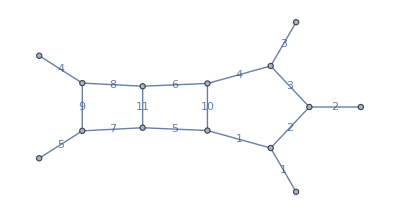

```mathematica
ContractPoint[expr_List,x_]:=ReplaceAll[expr,Join[Cases[expr,Labeled[a__,ToString@x]:>a],{Labeled[a__,ToString@x]:>Nothing}]]
ContractPoint[expr_List,x_List]:=Fold[ContractPoint,expr,x]
topgraphyqx=Flatten@{Map[Labeled[First@#,Last@#]&,List@@@Values[Last[AbsoluteOptions[topgraph,EdgeLabels]]]/.UndirectedEdge->Rule,{1}],Labeled@@@Transpose[{Sort[Select[Keys[Values[Last[AbsoluteOptions[topgraph,EdgeStyle]]]]/.UndirectedEdge->Rule,Keys[#]<=5&]],Range[5]}]}/.Subscript->Last;
GraphPlot[topgraphyqx]
```

```mathematica
Clear@vertex
vertex[graph_]:=Module[{data,vertexcoe},
data=FullGraphics[graph];
vertexcoe=Union[Cases[(data/.Graphics->First),Disk[{a_,b_},_]:>{a,b},Infinity]];
Transpose[{vertexcoe,Length[Cases[data[[1,1,1]],#,Infinity]]&/@vertexcoe}]
]
ExternalVertex[graph_]:=Module[{extline,extvex},
extvex=First/@Cases[vertex[graph],{{_,_},1}];
(*Print[extvex];*)
extline=Flatten[Cases[
FullGraphics[graph][[1,1,1]]
,Arrow[{a_,b_},_]:>{a,b}/;MemberQ[extvex,a]==True||MemberQ[extvex,b]==True
,Infinity],1];
(*Print[extline];*)
Length@Complement[extline,extvex]
]
```

```mathematica
topsec=Total[sectorindex[[-1]]];
graph=Table[GraphPlot[ContractPoint[topgraphyqx,First@Transpose[Position[Take[sectorindex[[i]],topsec],0]]],PlotLabel->Style[StringJoin["s",ToString[sectorid[[i]]],":F",ToString[Flatten[Position[sector,sectorid[[i]]]][[1]]]," #",ToString[misineachsec[[i]]]],Blue],ImageSize->Tiny,VertexCoordinates->{5->{-1,0},4->{-1,3},1->{4.3,-1},3->{4.3,4},2->{7.75,1.5}},GraphLayout->"SpringElectricalEmbedding"],{i,Length@sectorid-1}];
```

```mathematica
(*FeynPlot[sectorindex_]:=GraphPlot[ContractPoint[topgraphyqx,First@Transpose[Position[Take[sectorindex,topsec],0]]],ImageSize->Tiny,VertexCoordinates->{5->{-1,0},4->{-1,3},1->{4.3,-1},3->{4.3,4},2->{7.75,1.5}}]*)
```

```mathematica
(*kinematicstype=Table[ExternalVertex[graph[[i]]],{i,Length@graph}]*)
```

### All graph

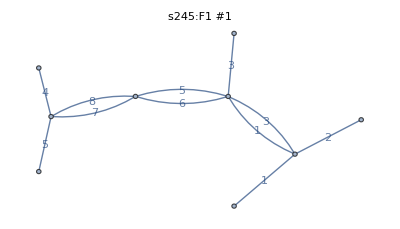
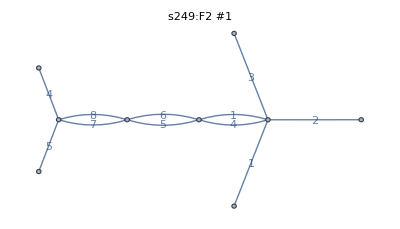
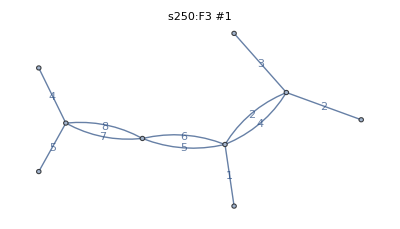
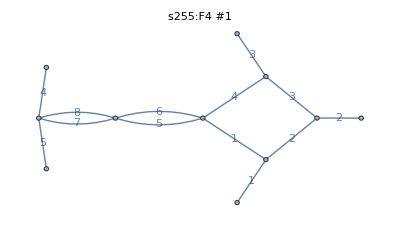
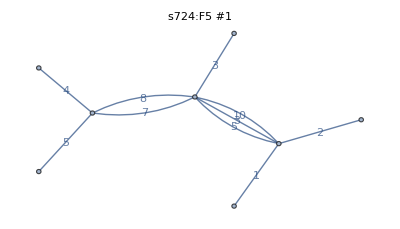
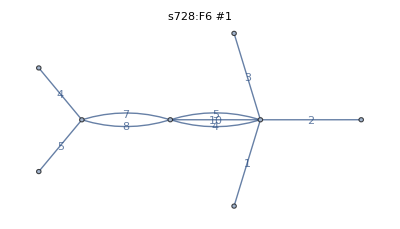
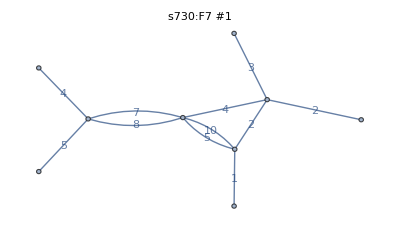
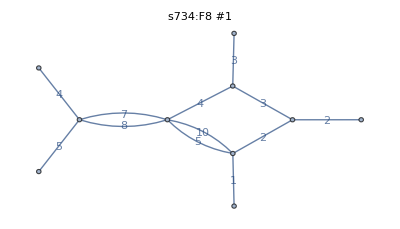
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
graph
```

```mathematica
Sort[sector][[{322,323}]]
```

{2047,2047}

### How to load UT

```mathematica
SetDirectory[NotebookDirectory[]];
var={s12,s23,s34,s45,s15};
mis=Get["MI_all.txt"]/.G->List;
sector=FromDigits[Reverse[Map[HeavisideTheta[#-1/2]&,#]],2]&/@mis;
sectorid=Union[sector];
sectorindex=Reverse[IntegerDigits[#,2,18]]&/@sectorid;
secid2index=Thread[sectorid->sectorindex];
misineachsec=Count[sector,#]&/@sectorid;
misbysec=Transpose[{sectorid,misineachsec}];
mis2sector=Thread[j@@@mis->sector];
mis=(First/@SortBy[mis2sector,Last]);
misrule=Table[mis[[i]]->UnitVector[Length@mis,i],{i,Length@mis}];
```

```mathematica
Clear[ut];
sol=Union[mis/.mis2sector];
Do[ut[id]=Get["~/Dropbox/my-dropbox/Project/3l5p-ut-searching/BBP/ut/"<>ToString[id]<>".m"],{id,sol}]
UT=Join[
ut[245],ut[249],ut[250],ut[255],ut[724],ut[728],ut[730],ut[734],ut[737],ut[738],ut[741],ut[743],ut[754],ut[756],ut[757],ut[758],ut[759],ut[762],ut[766],ut[1125],ut[1129],ut[1130],ut[1135],ut[1173],ut[1177],ut[1178],ut[1183],ut[1333],ut[1337],ut[1338],ut[1343],ut[1604],ut[1608],ut[1610],ut[1614],ut[1633],ut[1634],ut[1636],ut[1637],ut[1638],ut[1639],ut[1642],ut[1646],ut[1665],ut[1666],ut[1669],ut[1671],ut[1682],ut[1684],ut[1685],ut[1686],ut[1687],ut[1688],ut[1690],ut[1694],ut[1730],ut[1732],ut[1733],ut[1734],ut[1735],ut[1737],ut[1738],ut[1742],ut[1743],ut[1748],ut[1750],ut[1754],ut[1756],ut[1758],ut[1762],ut[1763],ut[1765],ut[1766],ut[1767],ut[1794],ut[1796],ut[1797],ut[1799],ut[1801],ut[1802],ut[1803],ut[1805],ut[1806],ut[1807],ut[1812],ut[1814],ut[1816],ut[1818],ut[1820],ut[1822],ut[1825],ut[1826],ut[1827],ut[1829],ut[1830],ut[1831],ut[1842],ut[1844],ut[1845],ut[1846],ut[1847],ut[1850],ut[1851],ut[1853],ut[1854],ut[1855],ut[1862],ut[1866],ut[1868],ut[1870],ut[1890],ut[1891],ut[1892],ut[1893],ut[1894],ut[1895],ut[1897],ut[1898],ut[1899],ut[1901],ut[1902],ut[1903],ut[1923],ut[1925],ut[1926],ut[1927],ut[1938],ut[1940],ut[1941],ut[1942],ut[1943],ut[1945],ut[1946],ut[1947],ut[1948],ut[1949],ut[1950],ut[1951],ut[1986],ut[1988],ut[1989],ut[1990],ut[1991],ut[1994],ut[1995],ut[1997],ut[1998],ut[1999],ut[2004],ut[2006],ut[2010],ut[2012],ut[2014],ut[2018],ut[2019],ut[2021],ut[2022],ut[2023],ut[2034],ut[2036],ut[2037],ut[2038],ut[2039],ut[2042],ut[2043],ut[2045],ut[2046],ut[2047]
];
```

```mathematica
ConstT=SparseArray[Get["/home/ustc/Dropbox/my-dropbox/Project/2047/ConstT.m"]];
```

```mathematica
(ConstT.UT)[[16]]
```

((s12+s23) s45 j[0,1,1,0,1,1,1,2,0,1,0,0,0,0,0,0,0,0])/e

```mathematica
(ConstT.UT)[[78]]
```

(s12+s23) j[0,1,1,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0]

```mathematica
j[0,1,1,0,1,0,1,1,0,1,1,0,0,0,0,0,0,0]/.mis2sector
```

1750

### Symmetry 326->316

```mathematica
sym=Get["/home/ustc/Project/3l5p/giant/uncut/reduce/NeatIBP-DE-no-sym/Add-Sym/outputs/family/results/IBP_all.txt"];
symrule=Solve[Thread[sym==0]][[1]]
```

{G[0,1,0,1,1,0,0,1,0,0,1,0,0,0,0,0,0,0]→G[0,1,0,1,0,1,1,0,0,0,1,0,0,0,0,0,0,0],G[1,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0]→G[0,0,0,1,0,0,1,0,0,1,1,0,0,0,0,0,0,0],G[1,0,0,0,0,1,0,0,1,1,1,0,0,0,0,0,0,0]→G[0,0,0,1,1,0,0,0,1,1,1,0,0,0,0,0,0,0],G[1,0,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0]→G[0,0,0,1,1,0,0,1,0,1,1,0,0,0,0,0,0,0],G[1,0,0,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0]→G[0,0,0,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0],G[1,0,0,1,0,1,1,0,0,0,1,0,0,0,0,0,0,0]→G[0,0,0,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0],G[1,0,0,1,1,0,0,1,0,0,1,0,0,0,0,0,0,0]→G[0,0,0,1,1,0,1,1,0,1,0,0,0,0,0,0,0,0],G[1,0,0,1,1,0,0,1,1,1,1,0,0,0,0,0,0,0]→G[1,0,0,1,0,1,1,0,1,1,1,0,0,0,0,0,0,0],G[1,0,1,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0]→G[1,0,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0],G[1,1,1,1,1,0,0,1,0,0,1,0,0,0,0,0,0,0]→G[1,1,1,1,0,1,1,0,0,0,1,0,0,0,0,0,0,0]}

```mathematica
Keys[symrule]/.G->j/.mis2sector
Values[symrule]/.G->j/.mis2sector
```

{1178,1665,1825,1633,737,1129,1177,1945,1173,1183}

{1130,1608,1816,1688,728,728,728,1897,1125,1135}

```mathematica
Table[
bc[Position[UT,ut[symrule[[i,1]]/.G->j/.mis2sector][[1]]][[1,1]]]->bc[Position[UT,ut[symrule[[i,2]]/.G->j/.mis2sector][[1]]][[1,1]]],{i,10}
]
```

{bc[27]→bc[23],bc[49]→bc[34],bc[114]→bc[106],bc[37]→bc[60],bc[9]→bc[6],bc[22]→bc[6],bc[26]→bc[6],bc[210]→bc[179],bc[25]→bc[21],bc[28]→bc[24]}

### Int 322

```mathematica
basisdef=Get["/home/yqx/Dropbox/Three-Loop-Five-Point-Feynman-Integral/2047/Results/BASIS_DEF.m"];
```

```mathematica
Get["/home/yqx/Dropbox/Three-Loop-Five-Point-Feynman-Integral/2047/Results/W1-integrals.m"][[322]]/.basisdef
```

1/3 Log[-W[1]]+1/3 Log[-W[2]]-3/2 Log[-W[3]]-7/6 Log[-W[4]]-3/2 Log[-W[5]]

```mathematica
Get["/home/yqx/Dropbox/Three-Loop-Five-Point-Feynman-Integral/2047/Results/W2-integrals.m"][[322]]/.basisdef
```

-(17 π^2)/24-11/12 Log[-W[1]]^2-1/2 Log[-W[1]] Log[-W[2]]-1/2 Log[-W[2]]^2-1/2 Log[-W[1]] Log[-W[3]]+Log[-W[2]] Log[-W[3]]+7/4 Log[-W[3]]^2+5/6 Log[-W[1]] Log[-W[4]]+Log[-W[2]] Log[-W[4]]+3/2 Log[-W[3]] Log[-W[4]]-2/3 Log[-W[4]]^2+Log[-W[1]] Log[-W[5]]-3/2 Log[-W[2]] Log[-W[5]]-Log[-W[3]] Log[-W[5]]+3/2 Log[-W[4]] Log[-W[5]]+9/4 Log[-W[5]]^2+1/6 PolyLog[2,W[11]/W[1]]+PolyLog[2,W[12]/W[2]]-PolyLog[2,W[13]/W[3]]-1/6 PolyLog[2,W[14]/W[4]]

```mathematica
Get["/home/yqx/Dropbox/Three-Loop-Five-Point-Feynman-Integral/2047/Results/W3-integrals.m"][[322]]/.basisdef
```

-1/6 π^2 Log[-W[1]]-31/18 Log[-W[1]]^3-1/6 π^2 Log[-W[2]]-1/4 Log[-W[1]]^2 Log[-W[2]]-1/4 Log[-W[1]] Log[-W[2]]^2-31/18 Log[-W[2]]^3+29/24 π^2 Log[-W[3]]+13/4 Log[-W[1]]^2 Log[-W[3]]+Log[-W[1]] Log[-W[2]] Log[-W[3]]+1/2 Log[-W[2]]^2 Log[-W[3]]+7/4 Log[-W[1]] Log[-W[3]]^2-3/2 Log[-W[2]] Log[-W[3]]^2-29/12 Log[-W[3]]^3+19/24 π^2 Log[-W[4]]+23/12 Log[-W[1]]^2 Log[-W[4]]+23/12 Log[-W[2]]^2 Log[-W[4]]-7/2 Log[-W[1]] Log[-W[3]] Log[-W[4]]-Log[-W[2]] Log[-W[3]] Log[-W[4]]-9/4 Log[-W[3]]^2 Log[-W[4]]+1/3 Log[-W[1]] Log[-W[4]]^2+1/3 Log[-W[2]] Log[-W[4]]^2+3/4 Log[-W[3]] Log[-W[4]]^2-2/9 Log[-W[4]]^3+29/24 π^2 Log[-W[5]]+1/2 Log[-W[1]]^2 Log[-W[5]]+Log[-W[1]] Log[-W[2]] Log[-W[5]]+13/4 Log[-W[2]]^2 Log[-W[5]]-Log[-W[1]] Log[-W[3]] Log[-W[5]]-Log[-W[2]] Log[-W[3]] Log[-W[5]]+5/2 Log[-W[3]]^2 Log[-W[5]]-Log[-W[1]] Log[-W[4]] Log[-W[5]]-7/2 Log[-W[2]] Log[-W[4]] Log[-W[5]]+Log[-W[3]] Log[-W[4]] Log[-W[5]]+3/4 Log[-W[4]]^2 Log[-W[5]]-3/2 Log[-W[1]] Log[-W[5]]^2+7/4 Log[-W[2]] Log[-W[5]]^2-1/2 Log[-W[3]] Log[-W[5]]^2-9/4 Log[-W[4]] Log[-W[5]]^2-17/12 Log[-W[5]]^3-1/12 π^2 Log[-W[16]]+1/2 Log[-W[1]] Log[-W[2]] Log[-W[16]]-1/2 Log[-W[1]] Log[-W[4]] Log[-W[16]]-1/2 Log[-W[2]] Log[-W[4]] Log[-W[16]]+1/4 Log[-W[4]]^2 Log[-W[16]]+1/4 Log[-W[4]] Log[-W[16]]^2-1/12 Log[-W[16]]^3-1/3 π^2 Log[-W[18]]+Log[-W[1]]^2 Log[-W[18]]-2 Log[-W[1]] Log[-W[3]] Log[-W[18]]-2 Log[-W[1]] Log[-W[4]] Log[-W[18]]+2 Log[-W[3]] Log[-W[4]] Log[-W[18]]+Log[-W[1]] Log[-W[18]]^2-1/3 Log[-W[18]]^3-1/3 π^2 Log[-W[19]]+Log[-W[2]]^2 Log[-W[19]]-2 Log[-W[2]] Log[-W[4]] Log[-W[19]]-2 Log[-W[2]] Log[-W[5]] Log[-W[19]]+2 Log[-W[4]] Log[-W[5]] Log[-W[19]]+Log[-W[2]] Log[-W[19]]^2-1/3 Log[-W[19]]^3-2/3 Log[-W[1]] PolyLog[2,W[11]/W[1]]+Log[-W[3]] PolyLog[2,W[11]/W[1]]-5/6 Log[-W[4]] PolyLog[2,W[11]/W[1]]-1/2 Log[-W[1]] PolyLog[2,-W[11]/W[2]]+1/2 Log[-W[4]] PolyLog[2,-W[11]/W[2]]+2 Log[-W[1]] PolyLog[2,W[11]/W[3]]-2 Log[-W[4]] PolyLog[2,W[11]/W[3]]-Log[-W[1]] PolyLog[2,W[12]/W[2]]-4 Log[-W[2]] PolyLog[2,W[12]/W[2]]+Log[-W[3]] PolyLog[2,W[12]/W[2]]+Log[-W[4]] PolyLog[2,W[12]/W[2]]+2 Log[-W[2]] PolyLog[2,W[12]/W[4]]-2 Log[-W[5]] PolyLog[2,W[12]/W[4]]-4 Log[-W[1]] PolyLog[2,-W[13]/W[1]]-Log[-W[2]] PolyLog[2,-W[13]/W[1]]+Log[-W[4]] PolyLog[2,-W[13]/W[1]]+Log[-W[5]] PolyLog[2,-W[13]/W[1]]+2 Log[-W[1]] PolyLog[2,-W[13]/W[4]]-2 Log[-W[3]] PolyLog[2,-W[13]/W[4]]-1/2 Log[-W[2]] PolyLog[2,W[14]/W[1]]+1/2 Log[-W[4]] PolyLog[2,W[14]/W[1]]-2/3 Log[-W[2]] PolyLog[2,-W[14]/W[2]]-5/6 Log[-W[4]] PolyLog[2,-W[14]/W[2]]+Log[-W[5]] PolyLog[2,-W[14]/W[2]]+2 Log[-W[2]] PolyLog[2,-W[14]/W[5]]-2 Log[-W[4]] PolyLog[2,-W[14]/W[5]]-2 Log[-W[3]] PolyLog[2,-W[15]/W[3]]+2 Log[-W[5]] PolyLog[2,-W[15]/W[3]]+14/3 PolyLog[3,W[11]/W[1]]+1/2 PolyLog[3,-W[11]/W[2]]+2 PolyLog[3,W[11]/W[3]]+22/3 PolyLog[3,-W[11]/W[4]]-5 PolyLog[3,W[12]/W[2]]+2 PolyLog[3,W[12]/W[4]]-PolyLog[3,-W[12]/W[5]]-5 PolyLog[3,-W[13]/W[1]]-PolyLog[3,W[13]/W[3]]+2 PolyLog[3,-W[13]/W[4]]-2 PolyLog[3,-(W[11] W[13])/(W[3] W[4])]+1/2 PolyLog[3,W[14]/W[1]]+14/3 PolyLog[3,-W[14]/W[2]]+22/3 PolyLog[3,W[14]/W[4]]+2 PolyLog[3,-W[14]/W[5]]-1/2 PolyLog[3,-(W[11] W[14])/(W[1] W[2])]-2 PolyLog[3,-(W[12] W[14])/(W[4] W[5])]-4 PolyLog[3,-W[15]/W[3]]-4 PolyLog[3,W[15]/W[5]]+1/2 PolyLog[3,W[11]/W[16]]+1/2 PolyLog[3,-W[14]/W[16]]-1/2 PolyLog[3,(W[11] W[14])/(W[4] W[16])]+2 PolyLog[3,-W[11]/W[18]]+2 PolyLog[3,W[13]/W[18]]-2 PolyLog[3,(W[11] W[13])/(W[1] W[18])]+2 PolyLog[3,-W[12]/W[19]]+2 PolyLog[3,W[14]/W[19]]-2 PolyLog[3,(W[12] W[14])/(W[2] W[19])]-(46 Zeta[3])/3

### B matrix

```mathematica
B=Get["~/Dropbox/Three-Loop-Five-Point-Feynman-Integral/2047/Results/B-Kernel.m"];
```

```mathematica
Get["~/Dropbox/Three-Loop-Five-Point-Feynman-Integral/2047/Results/Letter.m"]
basisdef=Get["~/Dropbox/Three-Loop-Five-Point-Feynman-Integral/2047/Results/BASIS_DEF.m"];
var={s12,s23,s34,s45,s15};
```

```mathematica
Variables[B]
```

{F[1,1],F[1,2],F[1,3],F[1,4],F[1,5],F[1,6],F[1,7],F[1,8],F[1,9],F[1,10],F[1,11],F[1,12],F[1,14],F[1,16],F[1,17],F[1,18],F[1,19],F[1,20],F[1,21],F[1,22],F[1,23],F[1,24],F[1,25],F[1,26],F[2,1],F[2,2],F[2,3],F[2,4],F[2,5],F[2,11],F[2,12],F[2,13],F[2,14],F[2,15],F[2,16],F[2,17],F[2,18],F[2,19],F[2,20],F[2,41],F[2,43],F[2,44],F[2,46],F[2,48],F[2,49],F[2,56],F[2,57],F[2,59],F[2,66],F[2,67],F[2,68],F[2,69],F[2,70],F[2,71],F[2,72],F[2,73],F[2,74],F[2,75],F[2,76],F[2,78],F[2,79],F[2,81],F[2,82],F[2,83],F[2,84],F[2,85],F[2,86],F[2,87],F[2,88],F[2,89],F[2,90],PolyLog[2,(W[1] W[2] (-1+W[27]))/(W[27] W[31])],PolyLog[2,(W[1] W[5] (-1+W[27]))/(W[27] W[31])],PolyLog[2,(W[11] W[19] (1-W[28]))/W[31]],PolyLog[2,-(W[1] W[3] (-1+W[28]))/(W[28] W[31])],PolyLog[2,(W[3] W[4] (-1+W[30]))/(W[30] W[31])],PolyLog[2,-(W[27] W[31])/(W[2] W[5] (-1+W[27]))],PolyLog[2,(W[1] W[4] (-1+W[26])+W[31])/(W[4] W[19] (-1+W[26]))],PolyLog[2,-(W[12] (W[4] (W[3]-W[5])-(W[4] ((W[3]-W[5]) W[5]+W[2] (W[3]+W[5])))/W[12]+(2 W[26] W[31])/(-1+W[26])))/(2 W[2] W[17] W[19])],PolyLog[2,(W[15] (W[3] W[25]-(W[28] W[31])/(-1+W[28])))/(W[3] W[17] W[20])]}

```mathematica
B2038=Get["~/Dropbox/Three-Loop-Five-Point-Feynman-Integral/The-Rocket/Results/B-kernel.m"];
```

```mathematica
Union[Cases[B2038,F[2,a_]/;a>40,Infinity]]
```

{F[2,41],F[2,43],F[2,44],F[2,46],F[2,48],F[2,49],F[2,51],F[2,53],F[2,54],F[2,56],F[2,57],F[2,59],F[2,66],F[2,67],F[2,68],F[2,69],F[2,70],F[2,71],F[2,72],F[2,73],F[2,74],F[2,75],F[2,76],F[2,78],F[2,79],F[2,81],F[2,82],F[2,83],F[2,84],F[2,85],F[2,86],F[2,87],F[2,88],F[2,89],F[2,90]}

```mathematica
Cases[%11,F[2,a_]/;a>40,Infinity]
```

{F[2,41],F[2,43],F[2,44],F[2,46],F[2,48],F[2,49],F[2,56],F[2,57],F[2,59],F[2,66],F[2,67],F[2,68],F[2,69],F[2,70],F[2,71],F[2,72],F[2,73],F[2,74],F[2,75],F[2,76],F[2,78],F[2,79],F[2,81],F[2,82],F[2,83],F[2,84],F[2,85],F[2,86],F[2,87],F[2,88],F[2,89],F[2,90]}

```mathematica
Table[F[2,i],{i,61,65}]/.basisdef
```

{PolyLog[2,W[19]/W[6]],PolyLog[2,W[20]/W[7]],PolyLog[2,W[16]/W[8]],PolyLog[2,W[17]/W[9]],PolyLog[2,W[18]/W[10]]}

```mathematica
Table[F[2,i],{i,51,55}]/.basisdef
```

{PolyLog[2,(W[9] W[11])/(W[1] W[16])],PolyLog[2,(W[10] W[12])/(W[2] W[17])],PolyLog[2,(W[6] W[13])/(W[3] W[18])],PolyLog[2,(W[7] W[14])/(W[4] W[19])],PolyLog[2,(W[8] W[15])/(W[5] W[20])]}